# Математическа статистика 2024-2025 учебна година доц. Петър Копанов

проверка на хипотези

изисква активиране на допълнителен пакет HypothesisTesting` :

## Хистограми

{162.379,174.946}

{-1.29133,1.72183}

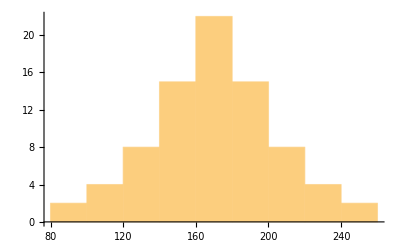

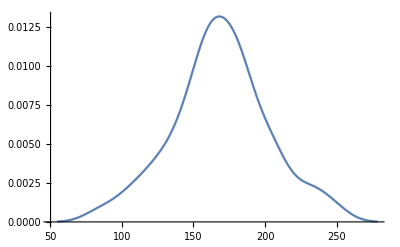

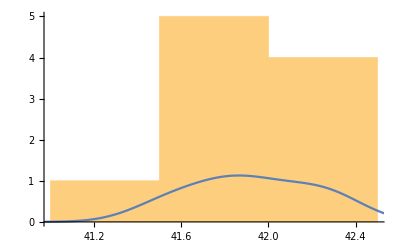

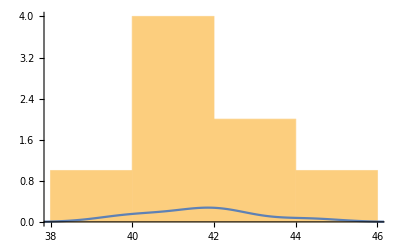

```mathematica
Clear["Global`*"]
 Needs["HypothesisTesting`"] 
datex1={111.,103.,251.,169.,213.,140.,224.,205.,166.,202.,227.,160.,234.,137.,186.,184.,163.,157.,181.,207.,189.,159.,180.,160.,196.,82.,107.,148.,155.,206.,192.,180.,205.,121.,199.,173.,177.,169.,93.,182.,127.,126.,187.,166.,200.,190.,171.,151.,166.,156.,187.,174.,164.,214.,139.,141.,178.,177.,243.,176.,186.,173.,182.,164.,162.,235.,164.,154.,156.,124.,149.,147.,116.,139.,129.,152.,175.,164.,141.,155.};StudentTCI[Mean[datex1],StandardDeviation[datex1]/Sqrt[Length[datex1]],Length[datex1],ConfidenceLevel->0.90]

set1={41.60,41.48,42.34,41.95,41.86,42.18,41.72,42.26,41.81,42.04};
set2={39.72,42.59,41.88,42.00,40.22,41.07,41.90,44.29};
MeanDifferenceCI[set1,set2,EqualVariances->False,ConfidenceLevel->0.98]

Histogram[datex1]
SmoothHistogram[datex1]
Show[Histogram[set1], SmoothHistogram[set1]]
Show[Histogram[set2], SmoothHistogram[set2]]
```

## Тест на знаците Тестът на знаците проверява дали медианите на две случайни извадки с равни дължини са равни. Ако не са равни тогава разпределенията на случайните величини са различни

```mathematica
Clear["Global`*"]
n=31; (* дължина на извадките *)
	(* табулация на вероятностите *)

TableForm[Table[{i, Sum[Binomial[n,k], {k, 0, i}]/2^n, N[Sum[Binomial[n,k], {k, 0, i}]/2^n]},{i, 0, n/2}]]
```

0 | 1/2147483648 | 4.65661×10^-10
1 | 1/67108864 | 1.49012×10^-8
2 | 497/2147483648 | 2.31434×10^-7
3 | 39/16777216 | 2.32458×10^-6
4 | 36457/2147483648 | 0.0000169766
5 | 6449/67108864 | 0.0000960976
6 | 942649/2147483648 | 0.000438955
7 | 6977/4194304 | 0.00166345
8 | 11460949/2147483648 | 0.00533692
9 | 988157/67108864 | 0.0147247
10 | 75973189/2147483648 | 0.0353778
11 | 1255043/16777216 | 0.0748064
12 | 301766029/2147483648 | 0.140521
13 | 15875597/67108864 | 0.236565
14 | 773201629/2147483648 | 0.36005
15 | 1/2 | 0.5

## ВАЖНО !!! тестът не различава различни разпределения с равни медиани, както показва примерът с data1- data3. Става въпрос за извадки на нормални разпределения с равни средни и медиани, но с различни дисперсии

0.484118

0.368202

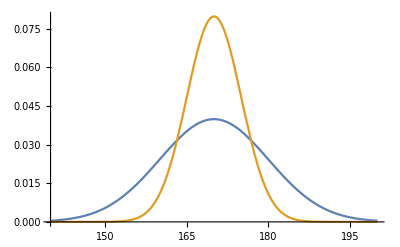

```mathematica
Clear["Global`*"]
data1=RandomVariate[NormalDistribution[170,10],100];            
data2=RandomVariate[NormalDistribution[170,10],100];      
data3=RandomVariate[NormalDistribution[170,5],100]; 
 SignTest[data1-data2]
 SignTest[data1-data3]
Plot[{PDF[NormalDistribution[170,10], x], PDF[NormalDistribution[170,5], x]}, {x, 140, 200}]
```

## Хи-квадрат тест на Пирсън

0.713595

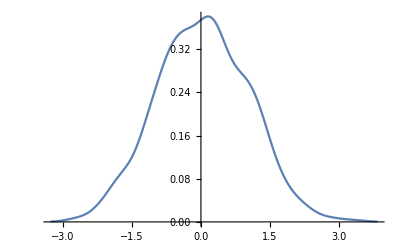

0.850263

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
Clear[data]
data=RandomVariate[NormalDistribution[0,1],600];
PearsonChiSquareTest[data,NormalDistribution[0,1]]
SmoothHistogram[data]
ShapiroWilkTest[data]
```

## тест за проверка за равенство на разпределенията на 2 извадки

0.595401

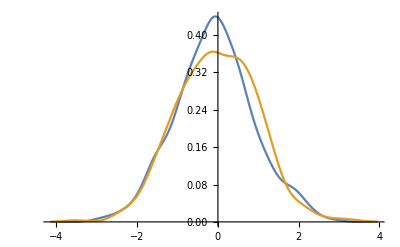

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data1=RandomVariate[NormalDistribution[0,1],400];
data2=RandomVariate[NormalDistribution[0,1],450];
PearsonChiSquareTest[data1,data2]
SmoothHistogram[{data1,data2}]
```

## проверяване нормалността на извадки с теста на Шапиро-Уилкс

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data1=RandomVariate[NormalDistribution[0,1],400];
data2=RandomVariate[NormalDistribution[0,1],450];
ShapiroWilkTest[data1]
ShapiroWilkTest[data2]
```

0.278725

0.702329

## Хи-квадрат тест на Пирсън 2 пример

0.00847398

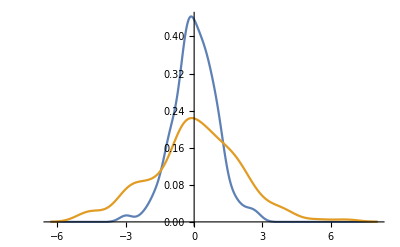

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data1=RandomVariate[NormalDistribution[0,1],100];
data2=RandomVariate[NormalDistribution[0,2],150];
PearsonChiSquareTest[data1,data2]
SmoothHistogram[{data1,data2}]
```

## тест на Колмогоров-Смирнов

0.955539

0.00131457

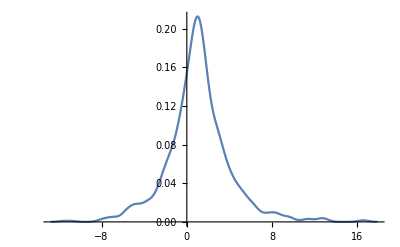

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[LaplaceDistribution[1,2],1000];
KolmogorovSmirnovTest[data,LaplaceDistribution[1,2]]
KolmogorovSmirnovTest[data,NormalDistribution[1,2]]
SmoothHistogram[data]
```

## тест на Колмогоров-Смирнов 2

0.0123865

0.649141

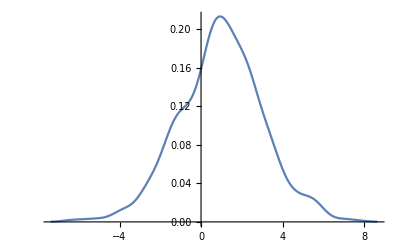

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[NormalDistribution[1,2],1000];
KolmogorovSmirnovTest[data,LaplaceDistribution[1,2]]
KolmogorovSmirnovTest[data,NormalDistribution[1,2]]
SmoothHistogram[data]
```

## тест на Колмогоров-Смирнов 3

0.441092

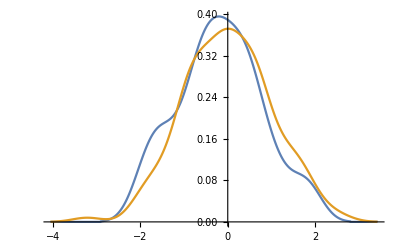

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data1=RandomVariate[NormalDistribution[0,1],100];
data2=RandomVariate[NormalDistribution[0,1],150];
KolmogorovSmirnovTest[data1,data2]
SmoothHistogram[{data1,data2}]
```

## Тест на Шапиро - Уилкс за нормално разпределени

0.00111476

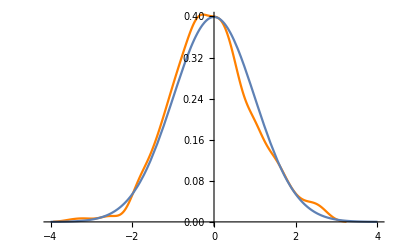

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[NormalDistribution[0,1],10^3];
ShapiroWilkTest[data]
Show[SmoothHistogram[data,PlotStyle->Orange],Plot[PDF[NormalDistribution[],x],{x,-4,4}],PlotRange->{0,.4}]
```

## проверка за нормалност на експоненциално разпределена извадка с тест на Шапиро - Уилкс

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data2=RandomVariate[ExponentialDistribution[1],50];
ShapiroWilkTest[data2]
ShapiroWilkTest[data2,"TestDataTable"]
```

8.75707×10^-7

| Statistic | P-Value
Shapiro-Wilk | 0.799978 | 8.75707×10^-7

## Тест на Андерсън-Дарлинг за нормалност на разпределение

0.602543

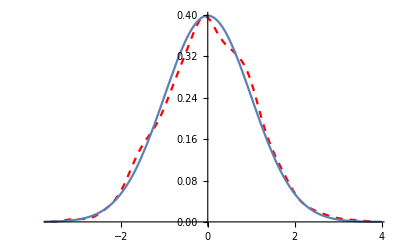

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[NormalDistribution[],10^3];
AndersonDarlingTest[data]
Show[SmoothHistogram[data,PlotStyle->{Dashed,Red}],Plot[PDF[NormalDistribution[],x],{x,-4,4}]]
```

## Тест на Андерсън-Дарлинг за нормалност на разпределение 2

3.89588×10^-6

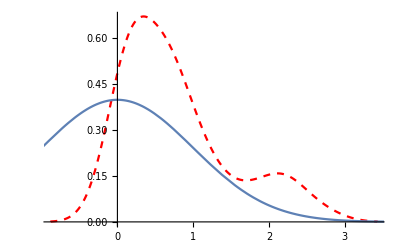

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data2=RandomVariate[ExponentialDistribution[1],50];
AndersonDarlingTest[data2]
Show[SmoothHistogram[data2,PlotStyle->{Dashed,Red}],Plot[PDF[NormalDistribution[],x],{x,-4,4}]]
```

## Тест на Андерсън-Дарлинг за разпределения, различни от нормалното

0.820644

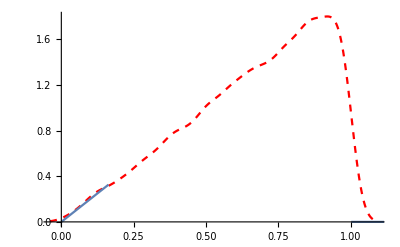

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[PowerDistribution[1,2],10^4];
AndersonDarlingTest[data,PowerDistribution[1,2]]
Show[SmoothHistogram[data,PlotStyle->{Dashed,Red}],Plot[PDF[PowerDistribution[1,2],x],{x,0,5}]]
```

## Задача 16.

0.436234

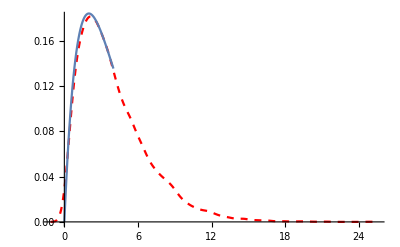

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[GammaDistribution[2,2],10^4];
AndersonDarlingTest[data,GammaDistribution[2,2]]
Show[SmoothHistogram[data,PlotStyle->{Dashed,Red}],Plot[PDF[GammaDistribution[2,2],x],{x,0,4}]]
```

## Задача 17.

0.634911

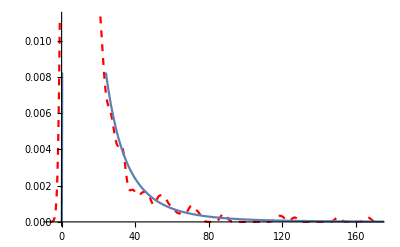

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[LogNormalDistribution[2,1],1000];
AndersonDarlingTest[data,LogNormalDistribution[2,1]]
Show[SmoothHistogram[data,PlotStyle->{Dashed,Red}],Plot[PDF[LogNormalDistribution[2,1],x],{x,0,200}]]
```

## Тест на Крамер-фон Мизес за нормално разпределение

0.690482

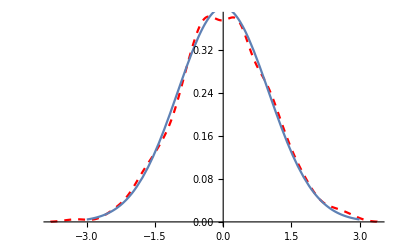

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[NormalDistribution[],10^3];
CramerVonMisesTest[data]
Show[SmoothHistogram[data,PlotStyle->{Dashed,Red}],Plot[PDF[NormalDistribution[0,1],x],{x,-3,3}]]
```

## Тест на Крамер-фон Мизес за разпределения, различни от нормалното

0.347918

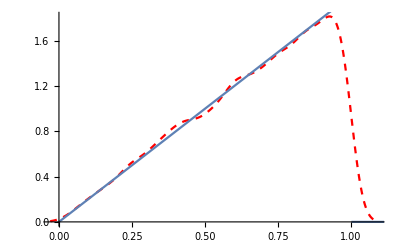

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[PowerDistribution[1,2],10^4];
CramerVonMisesTest[data,PowerDistribution[1,2]]
Show[SmoothHistogram[data,PlotStyle->{Dashed,Red}],Plot[PDF[PowerDistribution[1,2],x],{x,0,4}]]
```

## Задача 20.

0.269647

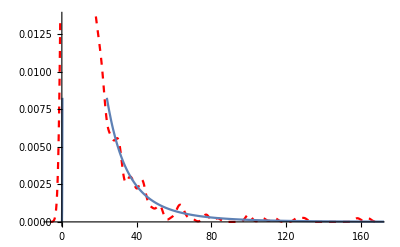

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[LogNormalDistribution[2,1],1000];
CramerVonMisesTest[data,LogNormalDistribution[2,1]]
Show[SmoothHistogram[data,PlotStyle->{Dashed,Red}],Plot[PDF[LogNormalDistribution[2,1],x],{x,0,200}]]
```

## сравняване на резултати от различни тестове за нормално разпределение сравняването между различните тестове става с помощта на командата DistributionFitTest сравнението на тестовете за нормално разпределение

0.114806

| Statistic | P-Value
Anderson-Darling | 0.716917 | 0.0602476
Baringhaus-Henze | 1.24841 | 0.0531401
Cramér-von Mises | 0.0990212 | 0.114806
Jarque-Bera ALM | 3.62037 | 0.16089
Kolmogorov-Smirnov | 0.0166171 | 0.09907
Kuiper | 0.0301129 | 0.0399672
Mardia Combined | 3.62037 | 0.16089
Mardia Kurtosis | 1.86279 | 0.0624923
Mardia Skewness | 0.0370556 | 0.847352
Pearson χ^2 | 40.5984 | 0.575992
Shapiro-Wilk | 0.998875 | 0.103822
Watson U^2 | 0.097756 | 0.0936105

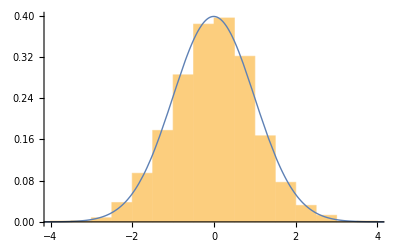

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[NormalDistribution[0,1],2500];
DistributionFitTest[data]
ℋ=DistributionFitTest[data,Automatic,"HypothesisTestData"];
ℋ["TestDataTable",All]
Show[Histogram[data,Automatic,"ProbabilityDensity"],Plot[PDF[ℋ["FittedDistribution"],x],{x,-5,5},PlotStyle->Thick]]
```

## Задача 22.

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[𝒹=ParetoDistribution[1,2],100];
DistributionFitTest[data,𝒹,{"TestDataTable","AndersonDarling"}]
```

| Statistic | P-Value
Anderson-Darling | 0.178484 | 0.995209

## Задача 23.

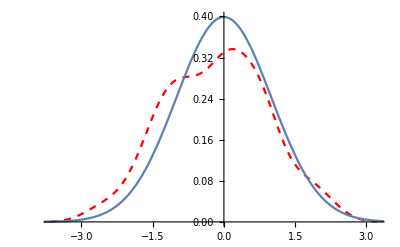
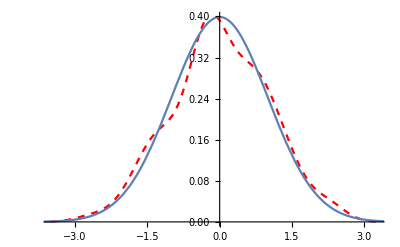

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"] 
data=RandomVariate[𝒟=BinormalDistribution[.5],100];
ℋ=DistributionFitTest[data,𝒟,"HypothesisTestData"];
Table[Show[SmoothHistogram[data⟦All,i⟧,PlotStyle->{Red,Dashed},PlotRange->{0,.4}],Plot[PDF[MarginalDistribution[𝒟,i],x],{x,-4,4}]],{i,2}]
```

## Задача 24.

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"]
```

## Задача 25.

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"]
```

## Задача 26.

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"]
```

## Задача 27.

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"]
```

## Задача 28.

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"]
```

## Задача 29.

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"]
```

## Задача 30.

```mathematica
Clear["Global`*"]
Needs["HypothesisTesting`"]
```